# Producer-Scrounger Model

## Food Blobs, Multi-Patch

January 11, 2012
Alexis Sparko

## Initializations

### Graphics

```mathematica
IMAGESIZE={400,400};
RANGE={-5,5};
RANGEPLUS={-6,6};
DIM=5;
```

### Populations

```mathematica
TOTALPOP = 40;
```

## Code

### Generate random points (locations for ducks, food)

```mathematica
randomPoint[range_]:=RandomReal[range,2];
randomPoints[n_,range_]:=Table[randomPoint[range],{n}];
```

Initialize some points to test out later on:

```mathematica
ducks=randomPoints[20,RANGE];
```

### Food Blobs

Makes n food blobs with centers c and radii r. If a non-zero radius is input into the function, it will use that radius for all the n blobs. If zero is input as the radius, it will choose random radii for each blob(between 5/10 and 10/10). Also, ensures that all blobs are initially spaced out with their x-coordinates so they don’t overlap.

```mathematica
makeFoodBlobs[n_,radius_]:= Module[{c1,c2,c,r,d},
d=2*DIM/n;
c1=Table[RandomReal[{-DIM+(d*(i-1)),-DIM+(d*i)}],{i,n}];
c2=RandomReal[RANGE,n];
c=Partition[Riffle[c1,c2],2];

If[radius==0,
r=Table[RandomInteger[{5,10},1]/10,{n}],
r=Table[radius,{n}]];
Partition[Riffle[c,Flatten[r]],2]
]
```

Initialize some Blobs to test code:

```mathematica
blobs=makeFoodBlobs[5,0];
```

### Basic Movement

#### Direction vectors

```mathematica
makeVectors[ducks_]:=Module[{num},
num=Length[ducks];
randomPoints[num,RANGE]
]
```

Initialize some vectors to test out code later on:

```mathematica
vecs = makeVectors[ducks];
```

#### Move in direction of vectors

```mathematica
(*ensures ducks keep moving in the same direction. only ducks who didn't eat will move*)
nextLoc[ducks_,vecs_,ifMoving_]:=Module[{normVecs,nextDucks},
nextDucks=ducks;
normVecs=Table[Normalize[vecs[[i]]],{i,Length[vecs]}];
Table[
If[ifMoving[[i]]==1,(* If they ate, move them *)
nextDucks[[i]]=nextDucks[[i]]-normVecs[[i]]/5,
nextDucks[[i]]=nextDucks[[i]]
],
{i,Length[nextDucks]}
]
]
```

#### Turn around if going to hit edge:

```mathematica
fixVectors[ducks_,vecs_,dim_]:=Module[{newvecs},
(* code to turn ducks around when they hit edges *)
newvecs=vecs;
Table[
If[ducks[[i]][[1]]≥dim,newvecs=ReplacePart[newvecs,i->{-newvecs[[i,1]],newvecs[[i,2]]}]],{i,1,Length[ducks]}];
Table[
If[ducks[[i]][[1]]≤-dim,newvecs=ReplacePart[newvecs,i->{-newvecs[[i,1]],newvecs[[i,2]]}]],{i,1,Length[ducks]}];
Table[
If[ducks[[i]][[2]]≥dim,newvecs=ReplacePart[newvecs,i->{newvecs[[i,1]],-newvecs[[i,2]]}]],{i,1,Length[ducks]}];
Table[
If[ducks[[i]][[2]]≤-dim,newvecs=ReplacePart[newvecs,i->{newvecs[[i,1]],-newvecs[[i,2]]}]],{i,1,Length[ducks]}];
newvecs
]
```

### Eat Food?

#### Check which ducks eat at each blob

Run this for each food blob with its respective radius

```mathematica
checkEat[ducks_,blob_,foodGrowth_]:=Module[{d,loc,radius,r,fedDucks,newBlob},
fedDucks={};
loc=blob[[1]];
radius=blob[[2]];

d=Table[EuclideanDistance[ducks[[i]],loc],{i,Length[ducks]}];

Table[
If[d[[i]]<radius || d[[i]]<0.1,(*if ducks are within blob, or close to a very small blob*)
fedDucks=Append[fedDucks,ducks[[i]]]],
{i,Length[ducks]}
];

If[Length[fedDucks]==0,(*If no ducks are eating blob*)
r=radius*foodGrowth,(*then food blob grows*)
If[Pi*radius^2-Length[fedDucks]*0.1<0,(*if ducks eat whole blob*)

{fedDucks=RandomSample[fedDucks,Ceiling[radius]],r=0},(*choose some of the ducks to feed and then remove blob*)

r=Sqrt[(Pi*radius^2-Length[fedDucks]*0.1)/Pi](*if ducks don't eat entire blob, shrink the blob by an amount in proportion to its radius*)
]
];

{fedDucks,r}
]
```

Test the checkEat function:

```mathematica
checkEat[{{5,3},{4.9,2.8},{4,1.5},{-3,-4},{-3.8,-5},{1,3}},{{4.75,2.77},0.9333},1.1]
```

{{{5,3},{4.9,2.8}},0.898547}

```mathematica
checkEat[{{3,-3},{1,1}},{{2.99,-3},0.01},1.1]
```

{{{3,-3}},0}

#### Get total ducks eating at all blobs, make new blobs if consumed

```mathematica
checkEatAll[ducks_,blobs_,foodGrowth_,blobRadius_]:=Module[{a,fedDucks,fedPos,r,numNew,blobLocs,blobsNext,newBlob},
numNew=0;
blobLocs=Table[blobs[[i,1]],{i,Length[blobs]}];

a=Table[checkEat[ducks,blobs[[i]],foodGrowth],{i,Length[blobs]}];
{fedDucks,r}={Partition[Flatten[Table[a[[i,1]],{i,Length[a]}]],2],Flatten[Table[a[[i,2]],{i,Length[a]}]]};fedPos=Flatten[Table[Position[ducks,fedDucks[[i]]],{i,Length[fedDucks]}],1];

blobsNext=Partition[Riffle[blobLocs,r],2];

Table[
If[r[[i]]==0,(* If an entire blob is consumed, ie if radius = 0 *)
newBlob=Flatten[makeFoodBlobs[1,blobRadius],1];(* Make a new blob *)
blobsNext=ReplacePart[blobsNext,i->newBlob]],
{i,Length[r]}];

{fedDucks,fedPos,blobsNext}
]
```

Test checkEatAll function:

```mathematica
{fedDucks,fedPos,blobs}=checkEatAll[ducks,blobs,1.1,1]
```

{{{-0.170575,2.55092},{0.206601,3.04088}},{{2},{9}},{{{-4.93299,-1.86359},0.55},{{-2.85679,4.58595},1.1},{{-0.3317,2.44804},0.967646},{{1.01742,-2.87799},0.66},{{4.76711,-2.83847},0.88}}}

### Update Satisfaction Levels and Movement Directions

#### updates prods and scroungers

checkSatisfactionMvt simultaneously adjusts a duck’s satisfaction value based on whether a duck ate any food, and also adjusts movement vectors for those ducks who can see food so that they move towards that food, or move scroungers towards producers they see.

```mathematica
checkSatisfactionMvt[ducks_,blobs_,radius_,satisfaction_,vecs_,ps_,fedPos_]:=Module[{prod,scroung,a, b,c,d,satisList,vecsTemp,vecsTempS,vecsNew,blobLocs,blobSize,blobPos,relevantRadii,ifMoving},

blobLocs=Table[blobs[[i,1]],{i,Length[blobs]}];
blobSize=Table[blobs[[i,2]],{i,Length[blobs]}];

prod=Pick[ducks,ps,1];
scroung=Pick[ducks,ps,0];

a=Table[Nearest[blobLocs,ducks[[i]],1],{i,1,Length[ducks]}]; (*list of food blob nearest to each duck*)
b=Table[EuclideanDistance[a[[i,1]],ducks[[i]]],{i,Length[ducks]}];(*distances between each duck and its nearest foodBlob*)
vecsTemp=Table[ducks[[i]]-a[[i,1]],{i,Length[ducks]}];(*move toward food*)

c=Table[Nearest[prod,ducks[[i]],1],{i,Length[ducks]}]; (*Nearest prod to each duck*)
d=Table[EuclideanDistance[c[[i,1]],ducks[[i]]],{i,Length[ducks]}]; (*dist bet each duck and nearest prod*)
vecsTempS=Table[ducks[[i]]-c[[i,1]],{i,Length[ducks]}];(*move toward prod*)

blobPos=Flatten[Table[Position[blobLocs,Flatten[a,1][[i]]],{i,Length[a]}],1];
relevantRadii=Extract[blobSize,blobPos];(*The radii of the blob that each duck is closest to*)
satisList=satisfaction;
vecsNew=vecs;
ifMoving=ps; (*producers will move, scroung won't, unless...*)

Table[
If[MemberQ[fedPos, {i}]==True, (*If that duck ate*)
{satisList=ReplacePart[satisList,i->1],vecsNew=ReplacePart[vecsNew,i->vecsTemp[[i]]],ifMoving=ReplacePart[ifMoving,i->1]},
If[b[[i]]-relevantRadii[[i]]<radius,(*If see food, go toward it*)
{satisList=ReplacePart[satisList,i->2*satisList[[i]]/3],vecsNew=ReplacePart[vecsNew,i->vecsTemp[[i]]],ifMoving=ReplacePart[ifMoving,i->1]},
If[ps[[i]]==1,(*If a producer*)
satisList=ReplacePart[satisList, i->2*satisList[[i]]/3],(*reduce that prod's status*)
If[d[[i]]<radius,(*Else,if scroung and see a prod*)
{satisList=ReplacePart[satisList,i->2*satisList[[i]]/3],vecsNew=ReplacePart[vecsNew,i->vecsTempS[[i]]],ifMoving=ReplacePart[ifMoving,i->1]},
satisList=ReplacePart[satisList, i->2*satisList[[i]]/3]
]
]
]
],{i,Length[ps]}];

{satisList,vecsNew,ifMoving} (*return status list and new movement vectors*)
]
```

```mathematica
ps=RandomInteger[{0,1},Length[ducks]]
```

{0,1,1,1,0,0,1,1,1,1,1,1,0,0,1,0,0,1,1,0}

### Change Foraging Strategy

#### Switch strategy based on satisfaction level. Be a producer with probability prodProb.

Here, ducks with low satisfaction levels might choose to switch strategies. Pick a 0 or 1 role (scroung or prod) based on their propensity to be a producer (prodProb value).

```mathematica
switchPS[prodProb_,ps_,satisfaction_]:=Module[{prodProbList,psList,satisList,decision},
prodProbList=prodProb;
psList=ps;
satisList=satisfaction;

Table[
If[satisList[[i]]<(2/3)^3,
psList=ReplacePart[psList,i->RandomVariate[BinomialDistribution[1,prodProbList[[i]]]]]
],{i,Length[satisList]}];

Table[
If[psList[[i]]≠ ps[[i]], (*If changing roles, renew satisfaction levels*)
satisList=ReplacePart[satisList,i->1]
],{i,Length[psList]}];

{psList,satisList}
]
```

Test switchPS

```mathematica
switchPS[{0.5,0.5,0.5,0.9},{1,1,1,1},{0.1,0.1,1,0.2}]
```

{{0,1,1,1},{1,0.1,1,0.2}}

#### Chance of switching based on level of dissatisfaction.

This version of the function to switch roles of a duck ensures ducks are more likely to switch roles based on how unhappy they are. If they do choose to switch roles, satisfaction level is renewed.

```mathematica
switchPS2[prodProb_,ps_,satisfaction_,thresh_]:=Module[{prodProbList,psList,satisList,decision,probSwitch},
prodProbList=prodProb;
psList=ps;
satisList=satisfaction;
decision=Table[0,{Length[ps]}];
probSwitch=Table[1-3*satisList[[i]],{i,Length[satisList]}];(*higher prob of switching if lower satisfaction level*)

Table[
If[satisList[[i]]<thresh,
decision=ReplacePart[decision,i->RandomVariate[BinomialDistribution[1,probSwitch[[i]]]]]
],{i,Length[satisList]}];
Table[
If[decision[[i]]==1,(*If decides to switch strategies*)
If[psList[[i]]==0, (*If switch and scrounger*)
{psList=ReplacePart[psList,i->1],satisList=ReplacePart[satisList,i->1]},
{psList=ReplacePart[psList,i->0],satisList=ReplacePart[satisList,i->1]}
]
],{i,Length[decision]}];


{psList,satisList}
]
```

```mathematica
switchPS2[{0.9,0.9,0.5,0.1},{1,1,1,1},{0.1,0.1,1,0.2}]
```

switchPS2[{0.9,0.9,0.5,0.1},{1,1,1,1},{0.1,0.1,1,0.2}]

#### Switch strategy based on satisfaction level THRESHOLD. Be a producer with probability prodProb. Just like switchPS, except we can change the threshold of satisfaction when they will switch roles.

Here, ducks with low satisfaction levels might choose to switch strategies. Pick a 0 or 1 role (scroung or prod) based on their propensity to be a producer (prodProb value).

```mathematica
switchPS3[prodProb_,ps_,satisfaction_,thresh_]:=Module[{prodProbList,psList,satisList,decision},
prodProbList=prodProb;
psList=ps;
satisList=satisfaction;

Table[
If[satisList[[i]]<thresh,
psList=ReplacePart[psList,i->RandomVariate[BinomialDistribution[1,prodProbList[[i]]]]]
],{i,Length[satisList]}];

Table[
If[psList[[i]]≠ ps[[i]], (*If changing roles, renew satisfaction levels*)
satisList=ReplacePart[satisList,i->1]
],{i,Length[psList]}];

{psList,satisList}
]
```

### Update Eaten

#### Keeps track of how many times each duck has eaten

```mathematica
updateEaten[eaten_,fedPos_]:=Module[{eatenNew},
eatenNew=eaten;
Table[
If[MemberQ[fedPos, {i}]==True, (*If that duck ate*)
eatenNew=ReplacePart[eatenNew,i->eatenNew[[i]]+1]
]
,{i,Length[eatenNew]}
];
eatenNew
]
```

```mathematica
updateEaten[ps,fedPos]
```

{0,2,1,1,0,0,1,1,2,1,1,1,0,0,1,0,0,1,1,0}

#### Keeps track total food eaten, separated by prod and scroungers (execute at each time step)

```mathematica
updateEaten2[eatenP_,eatenS_,fedPos_,ps_]:=Module[{eatenPNew,eatenSNew},
eatenPNew=eatenP;
eatenSNew=eatenS;

Table[
If[MemberQ[fedPos, {i}]==True, (*If that duck ate*)
If[ps[[i]]==1, (*If a producer that ate*)
eatenPNew=eatenPNew+1,
eatenSNew=eatenSNew+1
]
],{i,Length[ps]}
];
{eatenPNew,eatenSNew}
]
```

#### Creates separate values for Total Scrounger Food Eaten and Total Prod Food Eaten

```mathematica
breakEaten[eaten_,ps_]:=Module[{eatenP,eatenS},
eatenP=0;
eatenS=0;

eatenP=Total[Pick[eaten,ps,1]];
eatenS=Total[Pick[eaten,ps,0]];

{eatenP,eatenS}
]
```

### Update Distance

#### Keeps track of number of steps when duck has moved.

```mathematica
updateDistance[dist_,ifMoving_]:=Module[{distNew},
distNew=dist;

Table[
If[ifMoving[[i]]==1,
distNew=ReplacePart[distNew,i->distNew[[i]]+1]
],
{i,Length[ifMoving]}];

distNew
]
```

#### Creates separate values for Total Scrounger Dist and Total Prod Dist

```mathematica
breakDist[dist_,ps_]:=Module[{distP,distS},
distP=0;
distS=0;

distP=Total[Pick[dist,ps,1]];
distS=Total[Pick[dist,ps,0]];

{distP,distS}
]
```

#### Keeps track total dist, separated by prod and scroungers (execute at each time step)

```mathematica
updateDistance2[distP_,distS_,ifMoving_,ps_]:=Module[{distPNew,distSNew},
distPNew=distP;
distSNew=distS;

Table[
If[ifMoving[[i]]==1, (*If that duck is moving*)
If[ps[[i]]==1, (*If moving duck is a prod*)
distPNew=distPNew+1,
distSNew=distSNew+1
]
],{i,Length[ifMoving]}
];
{distPNew,distSNew}
]
```

## Graphics

### Graphics for Apps

#### Spatial Model

```mathematica
graphicsBlobs[ducks_,duckRadius_,satisfaction_,PS_,blobs_]:=
Graphics[{
Table[{GrayLevel[0.4],Disk[blobs[[i,1]],blobs[[i,2]]]},{i,Length[blobs]}],
Table[
If[PS[[i]]==1,
{Opacity[Max[satisfaction[[i]],0.3]],CMYKColor[1,0.01,0.20,0.03],PointSize[0.03],Point[ducks[[i]]],
Dashed,Circle[ducks[[i]],duckRadius]},
{Opacity[Max[satisfaction[[i]],0.3]],CMYKColor[0.1,1,0.22,0.01],PointSize[0.03],Point[ducks[[i]]],
Dashed,Circle[ducks[[i]],duckRadius]}],
{i,Length[ducks]}]},
PlotRange->{RANGEPLUS,RANGEPLUS},ImageSize->IMAGESIZE,Background->White]
```

#### Spatial Model plus Population Graphs

```mathematica
graphicsBlobsGraph[ducks_,duckRadius_,satisfaction_,PS_,blobs_,numProds_,numScroung_,numFood_]:= 
GraphicsRow[{
graphicsBlobs[ducks,duckRadius,satisfaction,PS,blobs],
ListLinePlot[{numProds,numScroung,numFood},AxesOrigin->{0,0},PlotStyle->{CMYKColor[1,0.01,0.20,0.03],CMYKColor[0.1,1,0.22,0.01],Gray}]},Frame->All,Background->White]
```

## App for Visualization: Random probability of switching foraging strategy

Producers and Scroungers will switch foraging strategies if unsuccessful at finding food.

```mathematica
appVaryingPop[numBlobs_,blobSize_,popsize_,probProdInit_]:=
Module[
{ducks,fedDucks,fedPos,hungryDucks,ps,blobs,satisfaction,switchingProb,eaten,dist,vecs,dim,ifMoving,numProds,numScroung,numFood},

satisfaction=Table[1,{popsize}];
eaten=Table[0,{popsize}];
dist=Table[0,{popsize}];
(*ps=RandomVariate[BinomialDistribution[1,probProdInit],{popsize}];*)
ps=Flatten[{Table[1,{Ceiling[popsize*probProdInit]}],Table[0,{popsize-Ceiling[popsize*probProdInit]}]}];
blobs=makeFoodBlobs[numBlobs,blobSize];
switchingProb=RandomReal[{0,1},popsize,WorkingPrecision->1];
numProds={Count[ps,1]};
numScroung={Count[ps,0]};
numFood={Total[Table[blobs[[i,2]],{i,Length[blobs]}]]*10};(*sum of blob size*)

ducks=randomPoints[popsize,RANGE];
vecs=makeVectors[ducks];
dim=5;

Manipulate[
graphicsBlobsGraph[ducks,radius,satisfaction,ps,blobs,numProds,numScroung,numFood],

(* ------------------- CONTROLS ---------------------- *)

Row[
{
Button["Next",
{fedDucks,fedPos,blobs}=checkEatAll[ducks,blobs,foodGrowth,blobSize];
{satisfaction,vecs,ifMoving}=checkSatisfactionMvt[ducks,blobs,radius,satisfaction,vecs,ps,fedPos];
eaten=updateEaten[eaten,fedPos];

ducks=nextLoc[ducks,vecs,ifMoving];
vecs=fixVectors[ducks,vecs,dim];
dist=updateDistance[dist,ifMoving];

{ps,satisfaction}=switchPS[switchingProb,ps,satisfaction];

numProds=Append[numProds,Count[ps,1]];
numScroung=Append[numScroung,Count[ps,0]];
numFood=Append[numFood,Total[Table[blobs[[i,2]],{i,Length[blobs]}]]*10];
],

Button["Food Eaten",
Print[eaten];
],

Button["Distance Traveled",
Print[dist];
],

Button["Switching Probabilities",
Print[switchingProb];
],

Button["Population Data",
Print["Num Prods", numProds,"Num Scroung",numScroung,"Food Amount", numFood];
],

Button["Reset",
satisfaction=Table[1,{popsize}];
eaten=Table[0,{popsize}];
dist=Table[0,{popsize}];
ps=RandomVariate[BinomialDistribution[1,probProdInit],{popsize}];
blobs=makeFoodBlobs[numBlobs,blobSize];
switchingProb=RandomReal[{0,1},popsize,WorkingPrecision->1];
numProds={Count[ps,1]};
numScroung={Count[ps,0]};
numFood={Total[Table[blobs[[i,2]],{i,Length[blobs]}]]*10};(*sum of blob size*)

ducks=randomPoints[popsize,RANGE];
vecs=makeVectors[ducks];
dim=5;
]
}],

(* ------------------- PARAMETERS -------------------- *)

{{radius,0.8,"Vision Radius"},0.5,2},
{{foodGrowth,1.05,"Food Growth Rate"},1,1.5}
(*{{scrPercentage,0.5,"Scrounger Percentage"},{0.25,0.5,0.75},ControlType->Setter}*)
]]
```

```mathematica
appVaryingPop[5,0,40,.9]
```

## Apps for Data Collection: Constant Populations

#### App data1: Total Food/Total Dist

```mathematica
data1[numBlobs_,blobSize_,popsize_,probProdInit_,foodGrowth_,radius_]:=
Module[
{ducks,fedDucks,fedPos,hungryDucks,ps,blobs,satisfaction,switchingProb,eaten,dist,vecs,dim,ifMoving,numProds,numScroung,numFood,distP,distS,eatenP,eatenS},

satisfaction=Table[1,{popsize}];
eaten=Table[0,{popsize}];
dist=Table[0,{popsize}];
ps=Flatten[{Table[1,{Ceiling[popsize*probProdInit]}],Table[0,{popsize-Ceiling[popsize*probProdInit]}]}];
blobs=makeFoodBlobs[numBlobs,blobSize];
switchingProb=RandomReal[{0,1},popsize,WorkingPrecision->1];
numProds={Count[ps,1]};
numScroung={Count[ps,0]};
numFood={Total[Table[blobs[[i,2]],{i,Length[blobs]}]]*10};(*sum of blob size*)

ducks=randomPoints[popsize,RANGE];
vecs=makeVectors[ducks];
dim=5;

(*Manipulate[
graphicsBlobsGraph[ducks,radius,satisfaction,ps,blobs,numProds,numScroung,numFood],
*)
(* ------------------- CONTROLS ---------------------- *)

Do[
{fedDucks,fedPos,blobs}=checkEatAll[ducks,blobs,foodGrowth,blobSize];
{satisfaction,vecs,ifMoving}=checkSatisfactionMvt[ducks,blobs,radius,satisfaction,vecs,ps,fedPos];
eaten=updateEaten[eaten,fedPos];

ducks=nextLoc[ducks,vecs,ifMoving];
vecs=fixVectors[ducks,vecs,dim];
dist=updateDistance[dist,ifMoving];

(*{ps,satisfaction}=switchPS[switchingProb,ps,satisfaction];*)

numProds=Append[numProds,Count[ps,1]];
numScroung=Append[numScroung,Count[ps,0]];
numFood=Append[numFood,Total[Table[blobs[[i,2]],{i,Length[blobs]}]]*10];
,{99}];

{distP,distS}=breakDist[dist,ps]; (*Can only do this at the end when constant population*)
{eatenP,eatenS}=breakEaten[eaten,ps];

Total[eaten]/Total[dist]
(*{eatenP/distP,eatenS/distS}*)
]
```

#### App data2: PopFood/PopDist

```mathematica
data2[numBlobs_,blobSize_,popsize_,probProdInit_,foodGrowth_,radius_]:=
Module[
{ducks,fedDucks,fedPos,hungryDucks,ps,blobs,satisfaction,switchingProb,eaten,dist,vecs,dim,ifMoving,numProds,numScroung,numFood,distP,distS,eatenP,eatenS},

satisfaction=Table[1,{popsize}];
eaten=Table[0,{popsize}];
dist=Table[0,{popsize}];
ps=Flatten[{Table[1,{Ceiling[popsize*probProdInit]}],Table[0,{popsize-Ceiling[popsize*probProdInit]}]}];
blobs=makeFoodBlobs[numBlobs,blobSize];
switchingProb=RandomReal[{0,1},popsize,WorkingPrecision->1];
numProds={Count[ps,1]};
numScroung={Count[ps,0]};
numFood={Total[Table[blobs[[i,2]],{i,Length[blobs]}]]*10};(*sum of blob size*)

ducks=randomPoints[popsize,RANGE];
vecs=makeVectors[ducks];
dim=5;

Do[
{fedDucks,fedPos,blobs}=checkEatAll[ducks,blobs,foodGrowth,blobSize];
{satisfaction,vecs,ifMoving}=checkSatisfactionMvt[ducks,blobs,radius,satisfaction,vecs,ps,fedPos];
eaten=updateEaten[eaten,fedPos];

ducks=nextLoc[ducks,vecs,ifMoving];
vecs=fixVectors[ducks,vecs,dim];
dist=updateDistance[dist,ifMoving];

(*{ps,satisfaction}=switchPS[switchingProb,ps,satisfaction];*)

numProds=Append[numProds,Count[ps,1]];
numScroung=Append[numScroung,Count[ps,0]];
numFood=Append[numFood,Total[Table[blobs[[i,2]],{i,Length[blobs]}]]*10];
,{99}];

{distP,distS}=breakDist[dist,ps]; (*Can only do this at the end when constant population*)
{eatenP,eatenS}=breakEaten[eaten,ps];

(*Total[eaten]/Total[dist]*)
{eatenP/distP,eatenS/distS}
]
```

## Data Collection: Constant Population, PopFood/PopDist, Varying Food Growth

#### Make Pop Energy Lists

```mathematica
makeEnergyPop[numBlobs_,blobSize_,popsize_,probProdInit_,foodGrowth_,radius_,n_]:=Module[{list},
list=Table[data2[numBlobs,blobSize,popsize,probProdInit,foodGrowth,radius],{n}];
list
]
```

### ~ 25% Producers. No switching.

5 Food Blobs
Start Blob Radius 1
40 Total Pop
Radius 1
1.05-1.5 Food Growth

#### Data Collection

```mathematica
(*Table[makeEnergyPop[5,1,40,0.25,i,1,20],{i,1.05,1.5,0.05}]*)
```

#### Data Storage

```mathematica
constPopEnergyFGRPop25={{{19/55,39/106},{331/990,339/902},{281/990,1/4},{172/495,929/2296},{23/66,17/46},{29/99,333/904},{34/99,232/661},{131/495,955/2716},{128/495,787/2603},{173/495,855/2753},{23/90,401/1298},{49/165,447/1331},{73/165,80/203},{40/99,275/893},{59/165,986/2699},{97/330,836/2681},{23/66,726/2357},{25/66,148/411},{19/55,819/2806},{173/495,49/171}},{{331/990,1046/2587},{40/99,944/2729},{148/495,404/1327},{37/110,1055/2649},{323/990,1157/2682},{41/99,497/1241},{239/495,1259/2534},{9/22,524/1315},{433/990,1394/2815},{40/99,610/1151},{107/330,973/2816},{457/990,1069/2418},{184/495,1051/2571},{301/990,744/2567},{181/495,1169/2770},{331/990,661/2689},{16/45,590/2653},{47/99,1198/2337},{166/495,971/2585},{259/990,553/1318}},{{51/110,103/246},{133/495,316/927},{349/990,1057/2766},{197/495,3/8},{7/18,1058/2735},{14/45,671/2381},{89/165,560/1377},{131/330,1187/2706},{73/198,953/2657},{26/45,1697/2633},{43/99,1247/2798},{29/110,408/1307},{83/165,885/2471},{193/495,439/1190},{164/495,1119/2720},{139/330,89/195},{503/990,734/1327},{53/165,284/953},{178/495,251/526},{437/990,1042/2745}},{{191/495,1045/2818},{343/990,932/2523},{59/198,756/2441},{149/330,520/921},{193/495,1423/2622},{181/495,617/1245},{16/55,443/1324},{431/990,134/281},{203/495,1285/2723},{89/198,429/772},{29/55,431/829},{103/198,473/904},{25/66,27/62},{37/99,1293/2843},{89/198,1193/2496},{196/495,1025/2597},{91/198,1223/2677},{151/330,1096/2583},{49/110,681/1264},{35/99,718/2459}},{{421/990,1236/2807},{469/990,703/1238},{119/330,133/436},{79/165,1075/2587},{283/495,75/127},{481/990,1079/2630},{41/99,991/2520},{37/66,254/483},{21/55,729/1424},{493/990,1331/2423},{239/990,886/2673},{343/990,965/2444},{184/495,985/2597},{179/495,286/609},{127/330,1136/2683},{151/330,659/1374},{62/165,963/2617},{233/495,652/1357},{233/495,1319/2646},{151/330,32/83}},{{13/33,1183/2684},{98/165,1616/2765},{569/990,1487/2719},{2/5,1237/2833},{223/495,1319/2610},{301/495,1754/2713},{133/330,933/2680},{529/990,1275/2462},{37/55,718/1121},{59/110,461/901},{431/990,1315/2603},{16/45,523/1293},{61/165,881/2637},{28/55,1390/2687},{469/990,599/1287},{113/198,1833/2872},{481/990,659/1266},{563/990,1653/2711},{409/990,143/335},{29/66,103/262}},{{43/90,221/398},{28/55,768/1319},{701/990,356/459},{151/330,507/1172},{22/45,243/520},{151/495,1102/2543},{601/990,104/179},{139/330,1299/2747},{274/495,1577/2713},{41/90,1201/2438},{17/45,938/2535},{533/990,1477/2676},{101/198,485/968},{119/198,1937/2777},{292/495,1643/2696},{82/165,1601/2805},{523/990,1777/2909},{293/990,886/2105},{104/165,1850/2709},{23/45,69/125}},{{53/90,967/1370},{232/495,691/1314},{499/990,1177/2498},{212/495,1476/2875},{191/495,1479/2761},{104/165,1259/2703},{307/495,1751/2664},{184/495,1182/2831},{541/990,687/1331},{262/495,1607/2662},{587/990,1708/2647},{3/5,841/1381},{47/90,400/663},{272/495,781/1373},{287/495,1469/2832},{503/990,93/173},{13/33,679/1334},{617/990,1563/2596},{299/495,1542/2581},{527/990,1873/2838}},{{248/495,1468/2771},{274/495,1194/2333},{457/990,1063/2599},{227/495,1331/2652},{61/165,670/1371},{521/990,1483/2249},{523/990,712/1419},{527/990,1648/2873},{409/990,1321/2685},{49/90,11/18},{224/495,1416/2803},{40/99,419/809},{299/495,612/911},{28/55,1565/2833},{79/198,1256/2827},{52/99,72/131},{50/99,878/1349},{593/990,1499/2643},{1/2,726/1373},{541/990,1511/2406}},{{53/90,1478/2851},{263/495,1655/2813},{173/330,97/163},{239/495,1532/2717},{613/990,1777/2691},{299/495,1658/2901},{79/198,1121/2728},{119/330,199/455},{6/11,586/1135},{74/165,1513/2491},{107/198,453/901},{397/990,200/399},{16/33,1535/2751},{277/495,1317/2665},{223/495,1490/2757},{17/33,1765/2609},{199/495,1081/2393},{613/990,1716/2507},{41/55,691/882},{236/495,497/901}}};
```

```mathematica
constPopEnergyFGRProd25 =Table[Table[constPopEnergyFGRPop25[[i,j,1]],{j,Length[constPopEnergyFGRPop25[[i]]]}],{i,Length[constPopEnergyFGRPop25]}];
```

```mathematica
constPopEnergyFGRScroung25 =Table[Table[constPopEnergyFGRPop25[[i,j,2]],{j,Length[constPopEnergyFGRPop25[[i]]]}],{i,Length[constPopEnergyFGRPop25]}];
```

#### Data Visualization

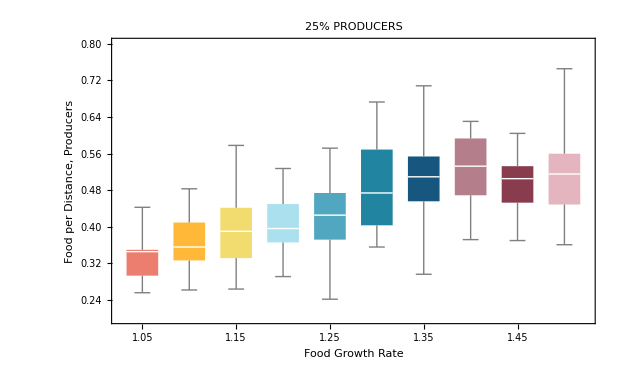

```mathematica
BW25ProdFGR=BoxWhiskerChart[constPopEnergyFGRProd25 ,ChartLabels->{Table[i,{i,1.05,1.5,0.05}]},ChartStyle->24,FrameLabel->{Style["Food Growth Rate",FontSize->18],Style["Food per Distance, Producers",FontSize->18]},PlotLabel->Style["25% PRODUCERS",Bold,Large,FontFamily->"Helvetica"],PlotRange->{0.2,.8},Background->White]
```

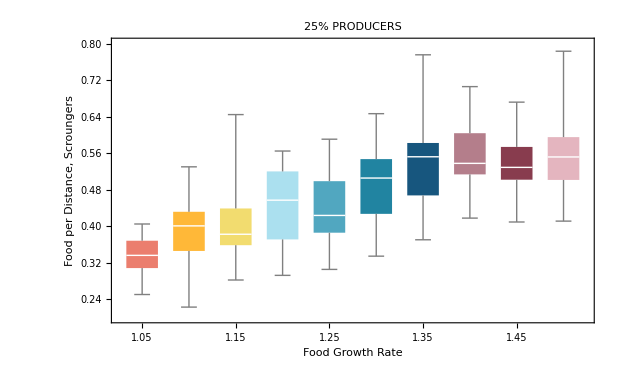

```mathematica
BW25ScroungFGR=BoxWhiskerChart[constPopEnergyFGRScroung25 ,ChartLabels->{Table[i,{i,1.05,1.5,0.05}]},ChartStyle->24,FrameLabel->{Style["Food Growth Rate",FontSize->18],Style["Food per Distance, Scroungers",FontSize->18]},PlotLabel->Style["25% PRODUCERS",Bold,Large,FontFamily->"Helvetica"],PlotRange->{0.2,.8},Background->White]
```

```mathematica
meanEnergyFGRProd25=Table[N[Mean[constPopEnergyFGRProd25[[i]]]],{i,Length[constPopEnergyFGRProd25]}]
```

{0.332071,0.371818,0.40197,0.409242,0.429444,0.489444,0.503182,0.52899,0.496667,0.514949}

```mathematica
meanEnergyFGRScroung25=Table[N[Mean[constPopEnergyFGRScroung25[[i]]]],{i,Length[constPopEnergyFGRScroung25]}]
```

{0.336116,0.394482,0.404726,0.450495,0.446035,0.499689,0.547077,0.563177,0.544752,0.560698}

```mathematica
meanEnergyFGRProd25Pairs=Partition[Riffle[Table[i,{i,1.05,1.5,0.05}],meanEnergyFGRProd25],2]
```

{{1.05,0.332071},{1.1,0.371818},{1.15,0.40197},{1.2,0.409242},{1.25,0.429444},{1.3,0.489444},{1.35,0.503182},{1.4,0.52899},{1.45,0.496667},{1.5,0.514949}}

```mathematica
meanEnergyFGRScroung25Pairs=Partition[Riffle[Table[i,{i,1.05,1.5,0.05}],meanEnergyFGRScroung25],2]
```

{{1.05,0.336116},{1.1,0.394482},{1.15,0.404726},{1.2,0.450495},{1.25,0.446035},{1.3,0.499689},{1.35,0.547077},{1.4,0.563177},{1.45,0.544752},{1.5,0.560698}}

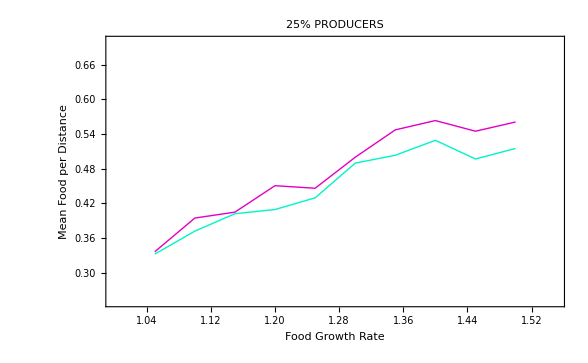

```mathematica
ListLinePlot[{meanEnergyFGRProd25Pairs,meanEnergyFGRScroung25Pairs},
Frame->True,
FrameLabel->{Style["Food Growth Rate",Bold,FontSize->18],Style["Mean Food per Distance",Bold,FontSize->18]},
(*PlotLegend->{"Producers","Scroungers"},
LegendPosition->{0.9,-0.4},
LegendShadow->None,*)
PlotRange->{{1,1.55},{0.25,0.7}},
PlotLabel->Style["25% PRODUCERS",Bold,Large,FontFamily->"Helvetica"],
PlotStyle->{Directive[CMYKColor[1,0.01,0.20,0.03],PointSize[.02],Thick],Directive[CMYKColor[0.1,1,0.22,0.01],PointSize[0.02],Thick]}]
(*prod blue, scroungers red*)
```

### ~ 50% Producers. No switching.

5 Food Blobs
Start Blob Radius 1
40 Total Pop
Radius 1
1.05-1.5 Food Growth

#### Data Collection

```mathematica
(*Table[makeEnergyPop[5,1,40,0.5,i,1,20],{i,1.05,1.5,0.05}]*)
```

#### Data Storage

```mathematica
constPopEnergyFGRPop50={{{23/66,353/983},{149/495,374/1855},{589/1980,467/1862},{307/990,368/1975},{23/66,172/609},{211/990,476/1831},{31/99,276/967},{257/990,652/1869},{17/44,612/1927},{181/660,559/1863},{101/330,2/7},{31/90,530/1621},{136/495,534/1901},{277/990,514/1919},{79/220,25/77},{127/396,633/1873},{11/45,509/1901},{25/99,523/1877},{623/1980,313/827},{13/44,423/1936}},{{631/1980,259/904},{683/1980,547/1888},{166/495,305/942},{551/1980,557/1688},{65/198,521/1900},{329/990,232/959},{689/1980,81/241},{113/330,219/895},{28/99,52/159},{601/1980,636/1777},{647/1980,567/1811},{119/396,396/1883},{67/165,321/953},{557/1980,259/947},{146/495,389/1754},{613/1980,20/61},{751/1980,650/1831},{19/55,842/1947},{581/1980,623/1959},{331/990,216/925}},{{127/396,673/1820},{259/660,739/1883},{691/1980,823/1870},{37/99,644/1891},{853/1980,101/229},{593/1980,565/1859},{893/1980,263/623},{7/18,644/1941},{73/220,322/969},{52/165,667/1930},{71/165,497/1833},{137/330,865/1886},{769/1980,469/1884},{184/495,881/1962},{641/1980,611/1746},{767/1980,585/1879},{661/1980,730/1859},{73/180,148/337},{119/396,655/1851},{769/1980,803/1888}},{{17/44,99/239},{677/1980,1033/1894},{7/18,838/1895},{9/22,665/1898},{97/198,883/1765},{367/990,348/931},{103/330,788/1963},{73/220,196/457},{89/220,804/1913},{433/990,792/1945},{343/990,687/1925},{83/220,771/1940},{32/99,564/1817},{79/220,175/387},{17/55,577/1822},{28/99,484/1911},{391/990,399/974},{419/990,829/1871},{73/180,855/1918},{38/99,740/1957}},{{377/990,437/964},{107/330,569/1916},{4/9,19/45},{1/3,275/633},{61/180,835/1826},{53/165,519/1886},{161/396,237/484},{46/99,563/936},{46/99,33/109},{329/660,968/1897},{347/660,955/1962},{199/495,244/625},{923/1980,85/188},{929/1980,177/377},{19/55,857/1876},{749/1980,769/1908},{929/1980,435/919},{947/1980,1038/1969},{659/1980,611/1939},{185/396,273/643}},{{883/1980,780/1921},{191/495,755/1929},{24/55,398/943},{32/99,499/1891},{19/36,1210/1913},{172/495,693/1867},{287/660,439/955},{761/1980,685/1933},{199/660,218/631},{167/396,414/959},{19/55,762/1957},{577/990,68/115},{139/330,751/1904},{707/1980,729/1859},{1079/1980,63/113},{257/660,553/1902},{851/1980,215/494},{901/1980,391/955},{73/180,1046/1881},{377/990,193/482}},{{763/1980,947/1925},{53/110,850/1863},{713/1980,675/1876},{301/660,1031/1941},{347/660,595/982},{47/110,546/1871},{563/990,109/186},{194/495,43/152},{7/12,1075/1781},{383/660,67/126},{97/220,409/959},{811/1980,17/43},{247/495,52/123},{427/990,198/475},{101/198,316/653},{91/180,1051/1950},{59/132,158/469},{53/132,646/1883},{157/495,609/1850},{497/990,31/75}},{{73/220,637/1938},{91/220,781/1924},{244/495,1136/1865},{361/990,613/1807},{238/495,895/1954},{272/495,145/253},{931/1980,829/1906},{233/660,28/57},{239/495,947/1906},{235/396,653/956},{959/1980,875/1838},{889/1980,902/1951},{911/1980,473/943},{15/44,43/115},{959/1980,151/314},{347/660,339/622},{833/1980,887/1862},{20/33,919/1818},{883/1980,329/927},{91/198,241/454}},{{73/165,759/1709},{751/1980,736/1931},{215/396,390/649},{233/495,532/955},{509/990,1095/1904},{86/165,1101/1882},{953/1980,908/1845},{1117/1980,1214/1855},{1181/1980,1123/1870},{229/495,825/1912},{169/330,1303/1829},{631/990,1137/1804},{109/220,232/485},{349/660,488/979},{197/396,1055/1928},{24/55,293/647},{49/90,543/952},{163/330,534/967},{91/180,1086/1907},{923/1980,903/1829}},{{208/495,113/242},{5/11,532/1719},{1189/1980,1025/1877},{2/3,56/87},{1151/1980,189/305},{7/18,893/1930},{98/165,1143/1871},{419/660,1122/1943},{31/66,511/985},{53/99,1073/1922},{272/495,851/1904},{1007/1980,876/1865},{77/180,682/1931},{16/33,1145/1772},{371/495,1287/1927},{5/9,1038/1961},{761/1980,734/1959},{487/990,1169/1917},{65/132,517/947},{157/330,413/902}}};
```

```mathematica
constPopEnergyFGRProd50 =Table[Table[constPopEnergyFGRPop50[[i,j,1]],{j,Length[constPopEnergyFGRPop50[[i]]]}],{i,Length[constPopEnergyFGRPop50]}];
```

```mathematica
constPopEnergyFGRScroung50 =Table[Table[constPopEnergyFGRPop50[[i,j,2]],{j,Length[constPopEnergyFGRPop50[[i]]]}],{i,Length[constPopEnergyFGRPop50]}];
```

#### Data Visualization

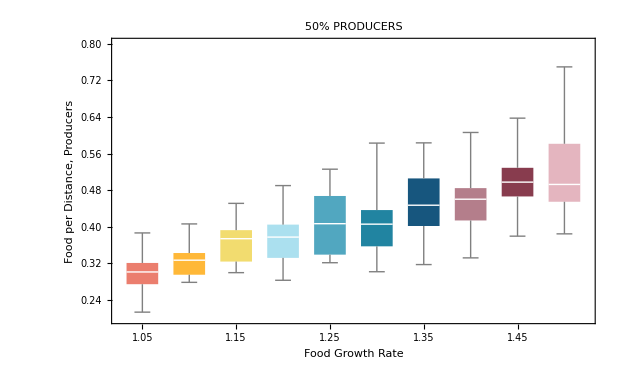

```mathematica
BW50ProdFGR=BoxWhiskerChart[constPopEnergyFGRProd50 ,ChartLabels->{Table[i,{i,1.05,1.5,0.05}]},ChartStyle->24,FrameLabel->{Style["Food Growth Rate",FontSize->18],Style["Food per Distance, Producers",FontSize->18]},PlotLabel->Style["50% PRODUCERS",Bold,Large,FontFamily->"Helvetica"],PlotRange->{0.2,.8},Background->White]
```

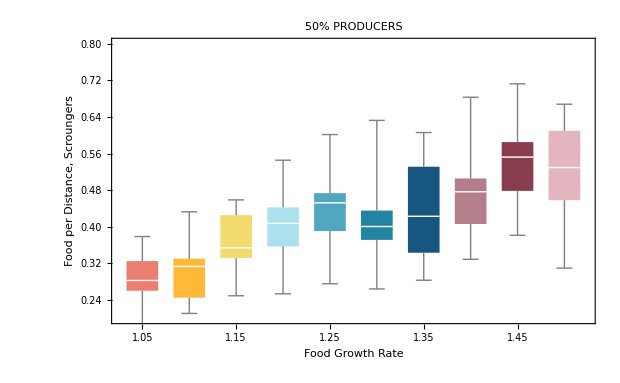

```mathematica
BW50ScroungFGR=BoxWhiskerChart[constPopEnergyFGRScroung50 ,ChartLabels->{Table[i,{i,1.05,1.5,0.05}]},ChartStyle->24,FrameLabel->{Style["Food Growth Rate",FontSize->18],Style["Food per Distance, Scroungers",FontSize->18]},PlotLabel->Style["50% PRODUCERS",Bold,Large,FontFamily->"Helvetica"],PlotRange->{0.2,.8},Background->White]
```

```mathematica
meanEnergyFGRProd50=Table[N[Mean[constPopEnergyFGRProd50[[i]]]],{i,Length[constPopEnergyFGRProd50]}]
```

{0.302197,0.324318,0.369899,0.373914,0.415581,0.416061,0.461237,0.46048,0.504646,0.523308}

```mathematica
meanEnergyFGRScroung50=Table[N[Mean[constPopEnergyFGRScroung50[[i]]]],{i,Length[constPopEnergyFGRScroung50]}]
```

{0.287979,0.301711,0.370989,0.402379,0.432122,0.424749,0.442399,0.476381,0.541367,0.520773}

```mathematica
meanEnergyFGRProd50Pairs=Partition[Riffle[Table[i,{i,1.05,1.5,0.05}],meanEnergyFGRProd50],2]
```

{{1.05,0.302197},{1.1,0.324318},{1.15,0.369899},{1.2,0.373914},{1.25,0.415581},{1.3,0.416061},{1.35,0.461237},{1.4,0.46048},{1.45,0.504646},{1.5,0.523308}}

```mathematica
meanEnergyFGRScroung50Pairs=Partition[Riffle[Table[i,{i,1.05,1.5,0.05}],meanEnergyFGRScroung50],2]
```

{{1.05,0.287979},{1.1,0.301711},{1.15,0.370989},{1.2,0.402379},{1.25,0.432122},{1.3,0.424749},{1.35,0.442399},{1.4,0.476381},{1.45,0.541367},{1.5,0.520773}}

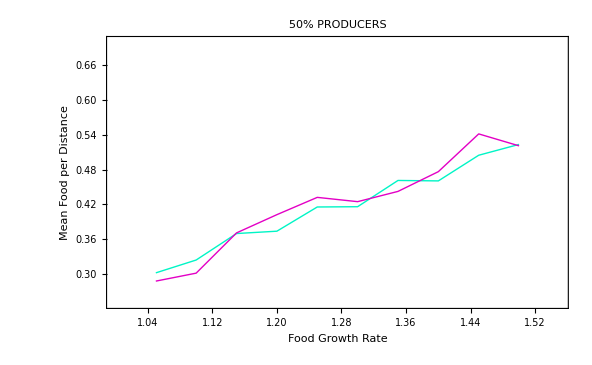

```mathematica
ListLinePlot[{meanEnergyFGRProd50Pairs,meanEnergyFGRScroung50Pairs},
Frame->True,
FrameLabel->{Style["Food Growth Rate",Bold,FontSize->18],Style["Mean Food per Distance",Bold,FontSize->18]},
(*PlotLegend->{"Producers","Scroungers"},
LegendPosition->{0.9,-0.4},
LegendShadow->None,*)
PlotRange->{{1,1.55},{0.25,0.7}},
PlotLabel->Style["50% PRODUCERS",Bold,Large,FontFamily->"Helvetica"],
PlotStyle->{Directive[CMYKColor[1,0.01,0.20,0.03],PointSize[.02],Thick],Directive[CMYKColor[0.1,1,0.22,0.01],PointSize[0.02],Thick]}]
(*prod blue, scroungers red*)
```

### ~ 75% Producers. No switching.

5 Food Blobs
Start Blob Radius 1
40 Total Pop
Radius 1
1.05-1.5 Food Growth

#### Data Collection

```mathematica
(*Table[makeEnergyPop[5,1,40,0.75,i,1,20],{i,1.05,1.5,0.05}]*)
```

#### Data Storage

```mathematica
constPopEnergyFGRPop75={{{289/990,247/959},{86/297,111/428},{181/495,255/932},{29/99,46/229},{293/990,64/247},{883/2970,341/925},{442/1485,297/917},{977/2970,146/483},{127/495,218/983},{74/297,109/486},{86/297,118/485},{514/1485,167/487},{833/2970,247/971},{5/18,295/983},{152/495,219/946},{175/594,194/983},{139/495,263/985},{491/1485,165/464},{541/1485,340/921},{311/990,146/495}},{{146/495,23/61},{499/1485,21/61},{739/2970,247/941},{46/165,325/874},{1093/2970,319/971},{941/2970,147/487},{977/2970,109/326},{323/990,166/495},{917/2970,251/912},{1003/2970,41/140},{943/2970,267/961},{329/990,291/962},{622/1485,131/315},{463/1485,175/491},{148/495,121/323},{997/2970,56/165},{542/1485,248/963},{943/2970,331/958},{508/1485,297/971},{167/495,285/932}},{{53/165,305/981},{247/594,406/983},{1123/2970,81/193},{205/594,28/93},{677/1485,443/922},{556/1485,365/947},{31/66,124/477},{79/270,116/483},{68/165,321/982},{641/1485,444/911},{1007/2970,315/964},{44/135,310/989},{488/1485,274/983},{49/165,97/328},{197/594,89/330},{188/495,479/943},{428/1485,71/326},{247/594,187/488},{25/66,21/64},{67/198,259/990}},{{17/55,239/886},{217/495,386/971},{466/1485,300/799},{608/1485,363/881},{479/1485,389/984},{508/1485,319/985},{184/495,413/964},{1/3,160/491},{46/135,295/973},{89/198,484/933},{347/990,193/477},{11/30,322/967},{953/2970,77/247},{1249/2970,355/943},{458/1485,27/85},{541/1485,109/330},{161/495,346/949},{221/594,41/109},{71/198,130/459},{482/1485,144/493}},{{1181/2970,317/985},{1/2,509/949},{698/1485,499/989},{1003/2970,329/986},{721/1485,431/975},{23/66,31/96},{502/1485,191/492},{205/594,393/980},{116/297,224/481},{13/45,113/301},{761/1485,169/330},{602/1485,352/975},{751/1485,587/976},{47/110,370/949},{49/165,385/942},{622/1485,387/961},{31/66,110/239},{1031/2970,85/326},{911/2970,283/918},{47/110,445/989}},{{226/495,152/495},{224/495,24/61},{83/198,559/982},{1429/2970,211/495},{1187/2970,201/479},{1153/2970,344/957},{203/495,359/888},{139/270,233/485},{47/135,323/973},{142/297,243/481},{347/990,301/983},{182/495,395/976},{29/66,215/494},{197/594,374/965},{1313/2970,469/974},{461/1485,305/919},{271/594,434/949},{214/495,201/460},{1031/2970,9/35},{631/1485,15/61}},{{172/495,305/962},{1171/2970,375/973},{17/33,214/495},{587/1485,361/828},{1223/2970,226/491},{764/1485,457/944},{179/495,191/495},{1171/2970,421/984},{449/990,344/939},{463/990,413/948},{658/1485,515/899},{1229/2970,31/80},{101/297,23/66},{511/990,493/953},{1123/2970,184/473},{371/990,405/974},{433/990,491/943},{103/297,192/493},{7/15,364/977},{598/1485,131/328}},{{736/1485,411/985},{1337/2970,188/495},{1373/2970,131/330},{29/55,172/309},{523/1485,292/985},{608/1485,29/55},{26/45,145/244},{287/594,271/478},{556/1485,116/327},{25/66,442/987},{613/1485,306/979},{1151/2970,297/989},{743/1485,484/953},{1361/2970,73/165},{19/33,542/957},{79/198,301/979},{706/1485,459/950},{784/1485,496/989},{80/297,289/930},{653/1485,127/322}},{{343/990,287/964},{56/135,380/963},{631/1485,169/466},{1249/2970,456/919},{46/99,480/977},{433/990,480/989},{161/330,79/165},{257/495,555/989},{469/990,386/981},{1757/2970,169/244},{1489/2970,222/487},{29/66,166/471},{1321/2970,313/972},{1259/2970,461/937},{1037/2970,239/953},{233/495,62/195},{19/45,403/913},{509/1485,361/957},{1193/2970,397/981},{1121/2970,367/940}},{{169/297,611/965},{529/990,233/488},{523/1485,113/323},{2009/2970,637/974},{74/165,379/943},{59/99,203/314},{1517/2970,273/488},{193/297,624/967},{581/1485,149/299},{689/1485,69/193},{763/1485,452/943},{746/1485,248/483},{1319/2970,195/487},{1273/2970,223/483},{7/18,423/850},{2143/2970,228/307},{11/27,191/495},{10/27,144/493},{1891/2970,107/192},{661/1485,158/307}}};
```

```mathematica
constPopEnergyFGRProd75 =Table[Table[constPopEnergyFGRPop75[[i,j,1]],{j,Length[constPopEnergyFGRPop75[[i]]]}],{i,Length[constPopEnergyFGRPop75]}];
```

```mathematica
constPopEnergyFGRScroung75 =Table[Table[constPopEnergyFGRPop75[[i,j,2]],{j,Length[constPopEnergyFGRPop75[[i]]]}],{i,Length[constPopEnergyFGRPop75]}];
```

#### Data Visualization

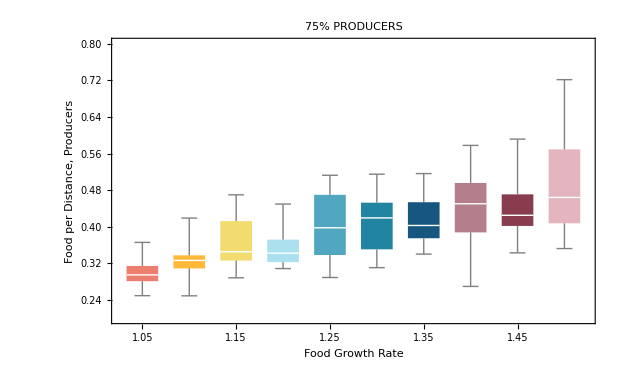

```mathematica
BW75ProdFGR=BoxWhiskerChart[constPopEnergyFGRProd75 ,ChartLabels->{Table[i,{i,1.05,1.5,0.05}]},ChartStyle->24,FrameLabel->{Style["Food Growth Rate",FontSize->18],Style["Food per Distance, Producers",FontSize->18]},PlotLabel->Style["75% PRODUCERS",Bold,Large,FontFamily->"Helvetica"],PlotRange->{0.2,.8},Background->White]
```

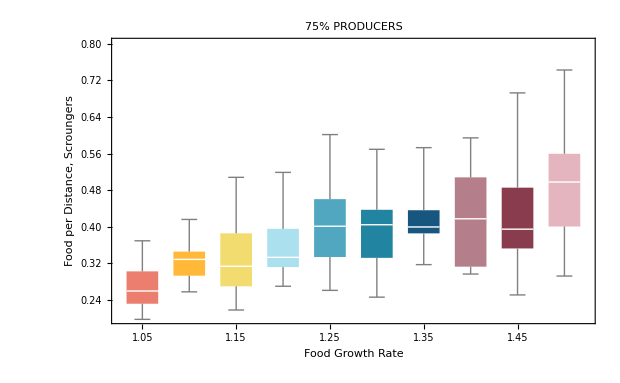

```mathematica
BW75ScroungFGR=BoxWhiskerChart[constPopEnergyFGRScroung75 ,ChartLabels->{Table[i,{i,1.05,1.5,0.05}]},ChartStyle->24,FrameLabel->{Style["Food Growth Rate",FontSize->18],Style["Food per Distance, Scroungers",FontSize->18]},PlotLabel->Style["75% PRODUCERS",Bold,Large,FontFamily->"Helvetica"],PlotRange->{0.2,.8},Background->White]
```

```mathematica
meanEnergyFGRProd75=Table[N[Mean[constPopEnergyFGRProd75[[i]]]],{i,Length[constPopEnergyFGRProd75]}]
```

{0.302559,0.326111,0.365993,0.357121,0.400976,0.412542,0.418754,0.447862,0.437727,0.502559}

```mathematica
meanEnergyFGRScroung75=Table[N[Mean[constPopEnergyFGRScroung75[[i]]]],{i,Length[constPopEnergyFGRScroung75]}]
```

{0.277381,0.325257,0.340402,0.357,0.41234,0.397069,0.422197,0.433248,0.422932,0.503427}

```mathematica
meanEnergyFGRProd75Pairs=Partition[Riffle[Table[i,{i,1.05,1.5,0.05}],meanEnergyFGRProd75],2]
```

{{1.05,0.302559},{1.1,0.326111},{1.15,0.365993},{1.2,0.357121},{1.25,0.400976},{1.3,0.412542},{1.35,0.418754},{1.4,0.447862},{1.45,0.437727},{1.5,0.502559}}

```mathematica
meanEnergyFGRScroung75Pairs=Partition[Riffle[Table[i,{i,1.05,1.5,0.05}],meanEnergyFGRScroung75],2]
```

{{1.05,0.277381},{1.1,0.325257},{1.15,0.340402},{1.2,0.357},{1.25,0.41234},{1.3,0.397069},{1.35,0.422197},{1.4,0.433248},{1.45,0.422932},{1.5,0.503427}}

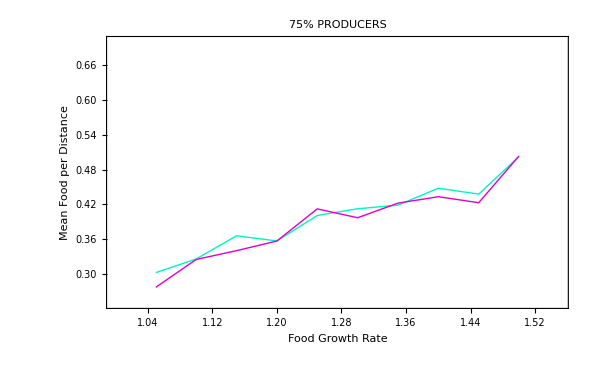

```mathematica
ListLinePlot[{meanEnergyFGRProd75Pairs,meanEnergyFGRScroung75Pairs},
Frame->True,
FrameLabel->{Style["Food Growth Rate",Bold,FontSize->18],Style["Mean Food per Distance",Bold,FontSize->18]},
(*PlotLegend->{"Producers","Scroungers"},
LegendPosition->{0.9,-0.4},
LegendShadow->None,*)
PlotRange->{{1,1.55},{0.25,0.7}},
PlotLabel->Style["75% PRODUCERS",Bold,Large,FontFamily->"Helvetica"],
PlotStyle->{Directive[CMYKColor[1,0.01,0.20,0.03],PointSize[.02],Thick],Directive[CMYKColor[0.1,1,0.22,0.01],PointSize[0.02],Thick]}]
(*prod blue, scroungers red*)
```

### ~ 100% Producers. No switching.

5 Food Blobs
Start Blob Radius 1
40 Total Pop
Radius 1
1.05-1.5 Food Growth

#### Data Collection

```mathematica
(*Table[makeEnergyTotal[5,1,40,1,i,1,20],{i,1.05,1.5,0.1}]*)
```

#### Data Storage

```mathematica
constPopFGREnergyTot100={{599/1980,1027/3960,619/1980,269/990,136/495,115/396,59/220,973/3960,115/396,191/660,137/440,283/990,283/990,148/495,71/220,1151/3960,1391/3960,1103/3960,61/198,331/1320},{133/396,133/440,29/66,1123/3960,223/792,7/22,146/495,841/3960,413/1320,239/792,287/990,589/1980,643/1980,11/36,1183/3960,49/132,409/1320,13/40,37/120,361/990},{151/495,113/264,147/440,257/660,107/264,1069/3960,83/220,679/1980,571/1980,59/165,16/55,85/264,1597/3960,10/33,85/264,131/396,697/1980,1303/3960,359/990,923/1980},{1361/3960,1121/3960,773/1980,281/792,857/1980,761/1980,151/440,247/660,155/396,115/264,1261/3960,1693/3960,37/120,1571/3960,56/165,18/55,1189/3960,421/1320,7/22,283/792},{373/990,1559/3960,403/990,23/60,152/495,1499/3960,103/330,43/132,295/792,257/660,371/1320,1451/3960,121/360,161/440,163/495,269/660,173/330,2/5,137/330,317/792},{1961/3960,1433/3960,17/44,1219/3960,1663/3960,1589/3960,1681/3960,1417/3960,189/440,479/1320,145/396,323/990,433/990,1447/3960,1403/3960,127/396,277/792,73/165,39/110,69/220},{1273/3960,427/990,1489/3960,1627/3960,32/99,103/330,49/120,79/220,1489/3960,1693/3960,1531/3960,833/1980,919/1980,403/990,307/792,161/495,23/66,149/396,1979/3960,1399/3960},{349/792,2161/3960,497/990,301/660,172/495,1181/1980,157/396,449/1320,1673/3960,419/1320,137/330,521/1320,497/1320,87/220,497/1320,301/792,61/180,829/1320,53/132,188/495},{1577/3960,1811/3960,1723/3960,4/11,1189/3960,43/120,727/1980,1657/3960,497/990,1349/3960,371/990,119/264,347/990,593/1320,1759/3960,41/120,257/660,1487/3960,181/396,569/792},{1363/3960,1543/3960,1273/1980,1531/3960,149/360,173/440,2443/3960,1481/3960,1987/3960,2491/3960,31/99,181/396,184/495,179/330,1891/3960,1889/3960,83/198,1499/3960,373/792,511/1320}};
```

#### Data Visualization

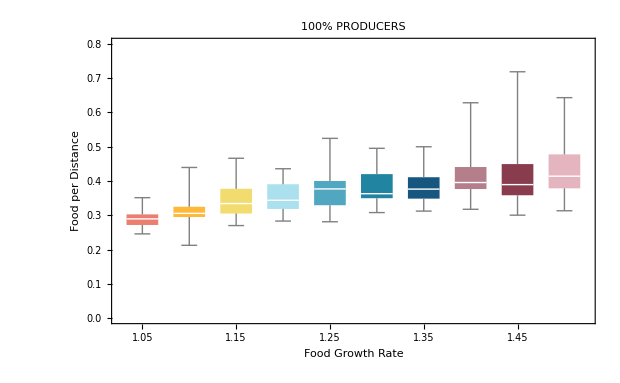

```mathematica
BW100food=BoxWhiskerChart[constPopFGREnergyTot100,ChartLabels->{Table[i,{i,1.05,1.5,0.05}]},ChartStyle->24,FrameLabel->{Style["Food Growth Rate",FontSize->18],Style["Food per Distance",FontSize->18]},PlotLabel->Style["100% PRODUCERS",Bold,Large,FontFamily->"Helvetica"],PlotRange->{0,0.8},Background->White]
```

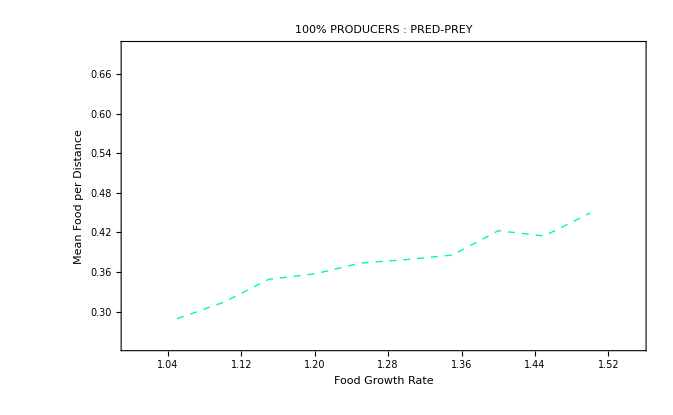

```mathematica
ListLinePlot[meanEnergyFGRTot100Pairs,
Frame->True,
FrameLabel->{Style["Food Growth Rate",Bold,FontSize->18],Style["Mean Food per Distance",Bold,FontSize->18]},
(*PlotLegend->{"Producers","Scroungers"},
LegendPosition->{0.9,-0.4},
LegendShadow->None,*)
PlotRange->{{1,1.55},{0.25,0.7}},
PlotLabel->Style["100% PRODUCERS : PRED-PREY",Bold,Large,FontFamily->"Helvetica"],
PlotStyle->{Directive[CMYKColor[1,0.01,0.20,0.03],PointSize[.02],Thick,Dashed]}]
(*prod blue, scroungers red*)
```

### COMPARISONS

#### Producers

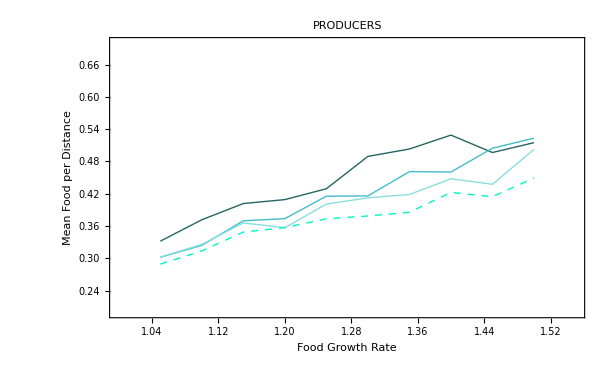

```mathematica
ListLinePlot[{meanEnergyFGRProd25Pairs,meanEnergyFGRProd50Pairs,meanEnergyFGRProd75Pairs,meanEnergyFGRTot100Pairs},
Frame->True,
FrameLabel->{Style["Food Growth Rate",Bold,FontSize->18],Style["Mean Food per Distance",Bold,FontSize->18]},
(*PlotLegend->{"Producers","Scroungers"},
LegendPosition->{0.9,-0.4},
LegendShadow->None,*)
PlotRange->{{1,1.55},{0.2,0.7}},
PlotLabel->Style["PRODUCERS",Bold,Large,FontFamily->"Helvetica"],
PlotStyle->{Directive[CMYKColor[0.66,0,0.02,0.6],Thick],Directive[CMYKColor[0.67,0.08,0,0.2],Thick],Directive[CMYKColor[0.38,0,0,0.13],Thick],Directive[CMYKColor[1,0.01,0.20,0.03],Dashed,Thick]}]
(*prod blue, scroungers red*)
```

#### Scroungers

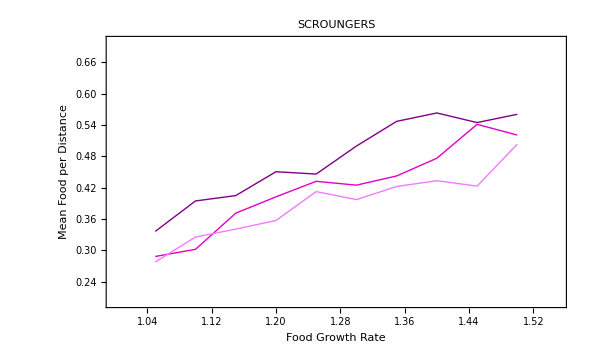

```mathematica
ListLinePlot[{meanEnergyFGRScroung25Pairs,meanEnergyFGRScroung50Pairs,meanEnergyFGRScroung75Pairs},
Frame->True,
FrameLabel->{Style["Food Growth Rate",Bold,FontSize->18],Style["Mean Food per Distance",Bold,FontSize->18]},
(*PlotLegend->{"Producers","Scroungers"},
LegendPosition->{0.9,-0.4},
LegendShadow->None,*)
PlotRange->{{1,1.55},{0.2,0.7}},
PlotLabel->Style["SCROUNGERS",Bold,Large,FontFamily->"Helvetica"],
PlotStyle->{Directive[CMYKColor[0.15,1,0.11,0.41],Thick],Directive[CMYKColor[0.1,1,0.22,0.01],Thick],Directive[CMYKColor[0.06,0.51,0,0],Thick]}]
(*prod blue, scroungers red*)
```